G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l77.0000.dat

λ0 = 77., cc = 10.147, 140 points

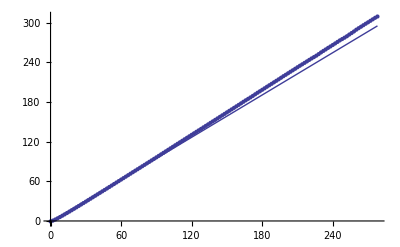
-Graphics- 300576.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l79.5000.dat

λ0 = 79.5, cc = 10.344, 85 points

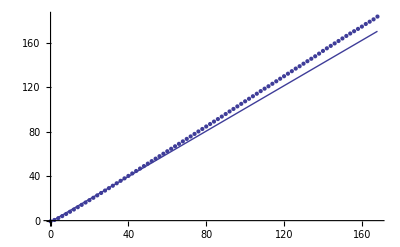
-Graphics- 297234.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l82.0000.dat

λ0 = 82., cc = 10.538, 59 points

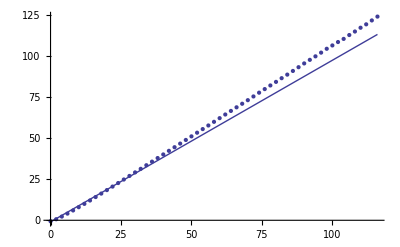
-Graphics- 295338.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l84.5000.dat

λ0 = 84.5, cc = 10.729, 54 points

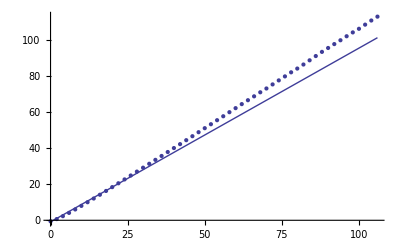
-Graphics- 263880.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l87.0000.dat

λ0 = 87., cc = 10.918, 45 points

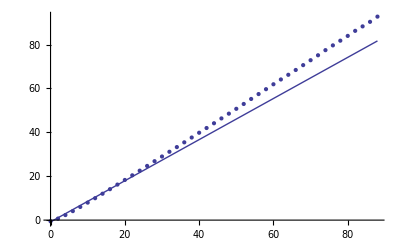
-Graphics- 252755.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l89.5000.dat

λ0 = 89.5, cc = 11.105, 42 points

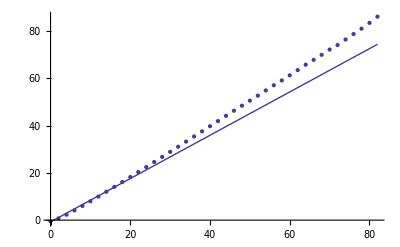
-Graphics- 222277.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l92.0000.dat

λ0 = 92., cc = 11.29, 39 points

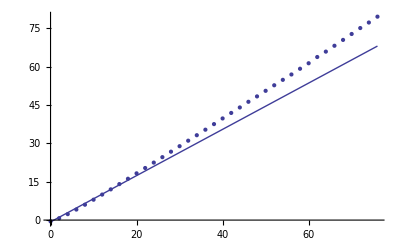
-Graphics- 213982.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l94.5000.dat

λ0 = 94.5, cc = 11.473, 33 points

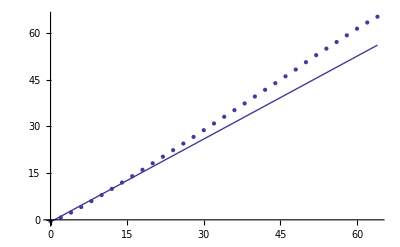
-Graphics- 218837.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l97.0000.dat

λ0 = 97., cc = 11.653, 32 points

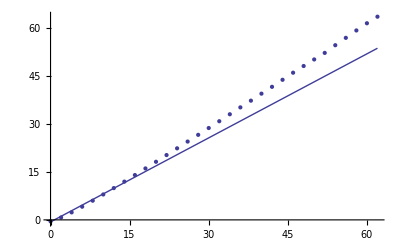
-Graphics- 202099.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l99.5000.dat

λ0 = 99.5, cc = 11.832, 32 points

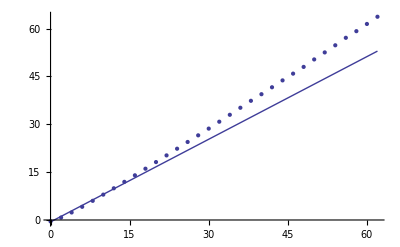
-Graphics- 177277.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l102.0000.dat

λ0 = 102., cc = 12.009, 27 points

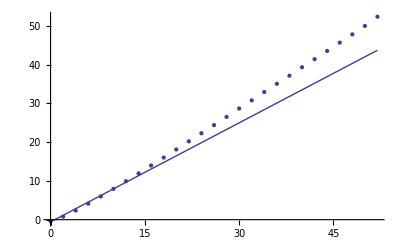
-Graphics- 187782.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l104.5000.dat

λ0 = 104.5, cc = 12.184, 26 points

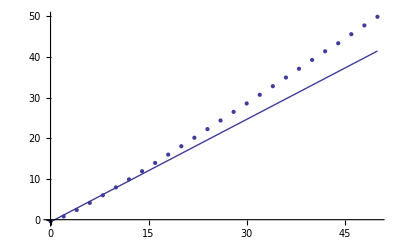
-Graphics- 172954.

G:\LAT\sd_metropolis\data\ssm\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l107.0000.dat

λ0 = 107., cc = 12.358, 26 points

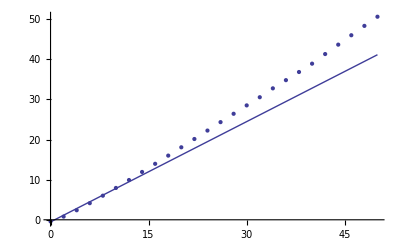
-Graphics- 161244.

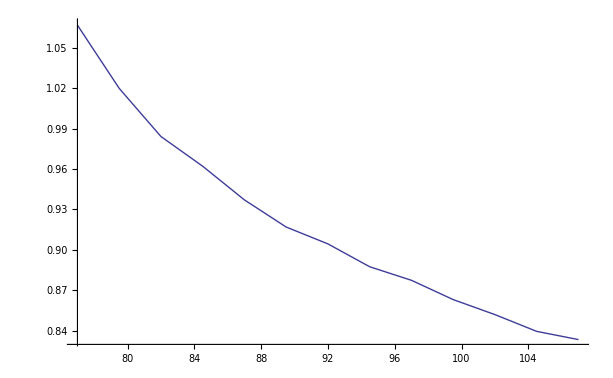

```mathematica
(* Some useful stuff *)
fsndig[x_,n_]:=ToString[PaddedForm[x,{n+2,n},NumberPadding->{"","0"}]];
Needs["ErrorBarPlots`"];
(* Advanced linear fitting *)
LinearFit[data_]:=Module[{mdata,xy,err,A,B,x,FFF,RP,A0,B0,RS,χ2dof},
mdata=Transpose[data];
xy=Transpose[{mdata[[1]],mdata[[2]]}];
err=mdata[[3]];
FFF=NonlinearModelFit[xy,A x + B,{A,B},x,Weights->1/err^2];
RP=FFF[{"BestFitParameters"}][[1]];
A0=A/.RP; B0=B/.RP;
RS=FFF["FitResiduals"];
(*Print[RS];*)
χ2dof=1/(Length[err]-1)Sum[RS[[i]]^2/err[[i]]^2,{i,1,Length[err]}];
{A0,B0,χ2dof}
];
(* Loop over stack stat files *)
SlopeList={};
For[λ0=77.0,λ0≤107.0,λ0+=2.5,
(*For[λ0=0.005,λ0≤0.085,λ0+=0.005,*)
StackStatFile="G:\\LAT\\sd_metropolis\\data\\ssm\\stack_stat_smod_d2_s16_m-4.00_nmc50000000_l"<>fsndig[λ0,4]<>".dat";
(*StackStatFile="G:\\LAT\\sd_metropolis\\data\\hmm\\stack_stat_l"<>fsndig[λ0,4]<>"_nmc10000000.dat";*)
Print[StackStatFile];
SData=Import[StackStatFile,"Table"];
cc=SData[[1,2]];
minx=SData[[1,1]];
maxx=SData[[1,1]];
Print["λ0 = ",λ0,", cc = ",cc,", ",Length[SData]," points"];
(* Plotting the data *)
DataToPlot=Table[
x=SData[[i,1]];
y=SData[[i,3]] (√cc)^x;
dy=SData[[i,4]](√cc)^x;
minx=Min[minx,x];
maxx=Max[maxx,x];
{{x,Log[y]},ErrorBar[dy/y]},{i,1,Length[SData]}];
GrA=ErrorListPlot[DataToPlot,PlotRange->All];
(* Fitting the data *)
DataToFit=Table[
x=SData[[i,1]];
y=SData[[i,3]](√cc)^x;
dy=SData[[i,4]](√cc)^x;
{x,Log[y],dy/y},{i,(*Round[Length[SData]/2]*)1,Length[SData]}];
{A0,B0,χ2}=LinearFit[DataToFit];
GrB=Plot[A0 x + B0,{x,minx,maxx}];
Print[Show[GrA,GrB]," ",χ2];
AppendTo[SlopeList,{λ0,A0}];
];
ListPlot[SlopeList,Joined->True,PlotRange->All]
```

```mathematica
N[1/60]
```

0.0166667

```mathematica
N[1/35]
```

0.0285714

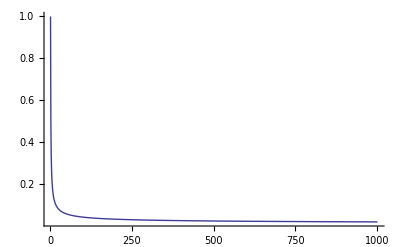

```mathematica
cg=1.0;
A=1; ν=1.2;
cgs={cg};
For[g=1,g≤1000,g++,
cg=cg/(1+ A/g^ν);
AppendTo[cgs,cg];
];
ListPlot[cgs,Joined->True,PlotRange->All]
```